/*=== === === === === === === === === === === === === === === === === === === *\
 *          ReaDDy - The Library for Reaction Diffusion Dynamics               *
 * === === === === === === === === === === === === === === === === === === === *
 *Copyright (c) 2010 - 2013, Johannes Schöneberg, Frank Noé, FU Berlin         *
 *All rights reserved.                                                         *
 *                                                                             *
 *Redistribution and use in source and binary forms, with or without           *
 *modification, are permitted provided that the following conditions are met : *
 *                                                                             *
 *     *Redistributions of source code must retain the above copyright         *
 *      notice, this list of conditions and the following disclaimer.          *
 *     *Redistributions in binary form must reproduce the above copyright      *
 *      notice, this list of conditions and the following disclaimer in the    *
 *      documentation and/or other materials provided with the distribution.   *
 *     *Neither the name of Johannes Schöneberg or Frank Noé or the FU Berlin  *
 *      nor the names of its contributors may be used to endorse or promote    *
 *      products derived from this software without specific prior written     *
 *      permission.                                                            *
 *                                                                             *
 *THIS SOFTWARE IS PROVIDED BY THE COPYRIGHT HOLDERS AND CONTRIBUTORS "AS IS"  *
 *AND ANY EXPRESS OR IMPLIED WARRANTIES, INCLUDING, BUT NOT LIMITED TO, THE    *
 *IMPLIED WARRANTIES OF MERCHANTABILITY AND FITNESS FOR A PARTICULAR PURPOSE   *
 *ARE DISCLAIMED.IN NO EVENT SHALL THE COPYRIGHT HOLDER OR CONTRIBUTORS BE     *
 *LIABLE FOR ANY DIRECT, INDIRECT, INCIDENTAL, SPECIAL, EXEMPLARY, OR          *
 *CONSEQUENTIAL DAMAGES (INCLUDING, BUT NOT LIMITED TO, PROCUREMENT OF         *
 *SUBSTITUTE GOODS OR SERVICES; LOSS OF USE, DATA, OR PROFITS; OR BUSINESS     *
 *INTERRUPTION) HOWEVER CAUSED AND ON ANY THEORY OF LIABILITY, WHETHER IN      *
 *CONTRACT, STRICT LIABILITY, OR TORT (INCLUDING NEGLIGENCE OR OTHERWISE)      *
 *ARISING IN ANY WAY OUT OF THE USE OF THIS SOFTWARE, EVEN IF ADVISED OF THE   *
 *POSSIBILITY OF SUCH DAMAGE.                                                  *
 *\=== === === === === === === === === === === === === === === === === === === */

5.91608

5.5

```mathematica
f=0.5 k (Sqrt[x^2+y^2+z^2]-x0)^2
```

0.5 k (-x0+√(x^2+y^2+z^2))^2

```mathematica
D[f,x]
```

(1. k x (-x0+√(x^2+y^2+z^2)))/(√(x^2+y^2+z^2))

```mathematica
dff=(1. k Abs[ (x1-x2)] (-x0+dist))/dist
```

(1. k (dist-x0) Abs[x1-x2])/dist

```mathematica
ff=0.5 k (-x0+x)^2
```

0.5 k (x-x0)^2

```mathematica
Energy
```

```mathematica
kk=10;
c1={1,2,3};
c2={6,5,4};
d=N[Norm[c1-c2]]
d0S=5.5
d0L=6.5
Print[nrg]
ff/.{k->kk,dist->d,x0->d0S,x->d}
ff/.{k->kk,dist->d,x0->d0L,x->d}
Print[grad];
{dff/.{k->kk,dist->d,x0->d0S,x1->c1[[1]],x2->c2[[1]]},
dff/.{k->kk,dist->d,x0->d0S,x1->c1[[2]],x2->c2[[2]]},
dff/.{k->kk,dist->d,x0->d0S,x1->c1[[3]],x2->c2[[3]]}}
{dff/.{k->kk,dist->d,x0->d0L,x1->c2[[1]],x2->c1[[1]]},
dff/.{k->kk,dist->d,x0->d0L,x1->c2[[2]],x2->c1[[2]]},
dff/.{k->kk,dist->d,x0->d0L,x1->c2[[3]],x2->c1[[3]]}}
```

5.91608

5.5

6.5

nrg

0.865612

1.70481

grad

{3.51652,2.10991,0.703303}

{-4.93503,-2.96102,-0.987005}

```mathematica
c1[[1]]-c2[[1]]
```

-5

```mathematica
10*5/5.9
```

8.47458

```mathematica
precompute=kk*(d-d0)/d
```

0.703303

```mathematica
precompute (c1[[1]]-c2[[1]])
```

-3.51652

```mathematica
5-d0
```

-0.5

0.865612

```mathematica
Gradient
```

{-16.1938,-9.7163,-3.23877}

```mathematica
Manipulate[Plot[xdiff(5+x)/x,{x,-5,5}],{xdiff,-1,1}]
```

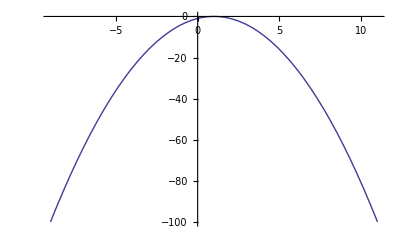

```mathematica
Plot[-(x-1)^2,{x,-9,11}]
```